# Uncertainty Estimation on Random Walk Problem with unequal P Value

Ziyang Gao
4/5/2018

## Instructor Notes

- This work is clearly incomplete. You have not finished the assignment, and do not have any commentary or code checks on the work you have done. I don’t know if this is because I said in class that you would have an opportunity to resubmit the problem, but “resubmit” does not mean “additional time to complete”, it means “revise”.

## What is the problem about

When the probability p that the particle goes right is not equal to the probability q = 1 − p that the particle goes left, we want to estimate the a and b values in estimation function E[x_n] = a + bp (When setting N = 20).

## Statistical functions

```mathematica
ave[myList_]:=Total[myList]/Length[myList]//N;
aveSqr[myList_]:=Total[myList^2]/Length[myList]//N;
var[myList_]:=aveSqr[myList]-ave[myList]^2;
unc[myList_]:=Sqrt[var[myList]/Length[myList]];
```

## Code for a single p value

### (a) Code for a Single x_N Run

```mathematica
n=20;
p=0.3;
steps[n_,p_]:=RandomChoice[{p,1-p}->{1,-1},n];
xValues[n_,p_]:=FoldList[Plus,0,steps[n,p]];
x[n_,p_]:=Last[xValues[n,p]];
```

code check:

```mathematica
steps[10,0.3]
xValues[10,0.3]
x[10,0.3]
```

{-1,1,-1,-1,-1,-1,1,-1,-1,-1}

{0,-1,-2,-3,-4,-3,-2,-3,-2,-3,-2}

-4

### (b) Code for an Ensemble of x_N Values

```mathematica
{n,p,numSamples}={20,0.3,100};
ensembleX[n_,p_,numSamples_]:=Table[x[n,p],{numSamples}];
ensembleList=ensembleX[n,p,numSamples];
```

code check:

```mathematica
ensembleX[10,0.3,10]
```

{-2,2,-6,-2,-4,-6,-10,0,-4,0}

### (c) Code for an Ensemble Average for the Final Positions

```mathematica
Clear[findEnsembleAve];
findEnsembleAve[n_,p_,numSamples_]:=
Module[
{temp},
temp=ensembleX[n,p,numSamples];
{p,ave[temp]}
];
findEnsembleAve[10,0.3,10]
```

{0.3,-3.6}

## Results for a Range of p Values

### (a) Final values

```mathematica
valuesFinal=List[];
{n,numSamples}={20,100};
For[p=0.1,p<1,AppendTo[valuesFinal,findEnsembleAve[n,p,numSamples]];p=p+0.1]
valuesFinal
```

(0.1 | -15.82
0.2 | -11.64
0.3 | -7.38
0.4 | -3.84
0.5 | 0.06
0.6 | 4.98
0.7 | 7.84
0.8 | 11.38
0.9 | 16.)

### (b) Linear fit: a + bp

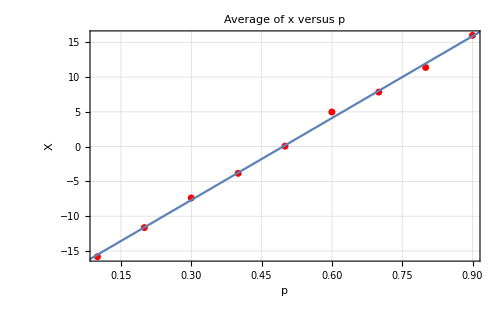

| Estimate | Standard Error | t-Statistic | P-Value
1 | -19.4578 | 0.31856 | -61.0803 | 8.27814×10^-11
p | 39.2667 | 0.566097 | 69.3639 | 3.40312×10^-11

39.2667 p-19.4578

{0.31856,0.566097}

```mathematica
line=Fit[valuesFinal,{1,p},p];
plot1=ListPlot[valuesFinal,PlotStyle->{RGBColor[1,0,0],PointSize[0.01]},Frame->True,FrameLabel->{"p","X"},PlotRange->All,PlotLabel->Style["Average of  x  versus  p",FontFamily->"Helvetica",FontSize->12,FontWeight->"Bold"],GridLines->Automatic,ImageSize->500];
plot2=Plot[line,{p,0,1}];
Show[plot1,plot2]
model=LinearModelFit[valuesFinal,p,p];
model["ParameterTable"]
model["BestFit"]
model["ParameterErrors"]
```

-19.4578 + 39.2667 p

## Conclusion and Speculation

The  linear relation between the probability and expectation of final position X is X= -19.5+ 39.2 p. A sample size of 100 in this 20 step random walk simulation could reduce the uncertainty of a and b to less than 1.